```mathematica
(1) 创建一个新笔记本，添加一个写着 "第一次作业" 的新标题单元.
(2) 突出选中单词 ￿第一次 ￿并将文本改成蓝色黑体.
(3) 将光标放在标题单元之下并使用单元插入助手来创建含有 "计算练习" 文本的新章节单元.
(4) 在笔记本底部添加一个写着 "解方程" 的节单元.
(5) 在节单元之下，创建一个自由格式输入单元来求解方程12x+24=0.
(6) 使用自由格式输入计算n 的和，其中n 从 1 到 10.
(7) 使用自由格式输入, 让 Mathematica 把第 100 个质数和第 108 个质数相乘.
(8) 判断 611 是否大于3^6.
(9) 使用自由格式输入绘制sin x+cosy的图形, 使用函数建议去除图像中的网格.
```

# 第一次作业

## 计算练习

## 解方程

WolframAlphaQueryParseResults

{{x→-2}}

WolframAlphaQueryParseResults

55

WolframAlphaQueryParseResults

320813

WolframAlphaQueryParseResults

False

WolframAlphaQueryParseResults

-Graphics3D-

```mathematica
Plot3D[Sin[x]+Cos[y],{x,-6.3,6.3},{y,-6.3,6.3},Mesh->None]
```

-Graphics3D-

# 习题1

1. (4)

```mathematica
N[Log[1+E^(-2)],10]
```

0.126928011

1. (6)

```mathematica
N[Sqrt[Abs[Log[Sin[35Degree]]]],10]
```

0.7455629221

1. (8)

```mathematica
N[Tan[ArcTan[Sqrt[2]/2]+I Sin[Sqrt[2]/3]],10]
```

0.531170653+0.5850327914 ⅈ

2.

```mathematica
GCD[861,1638,2415]
```

21

3.

```mathematica
LCM[48,105,120]
```

1680

4.

```mathematica
Binomial[10,3]
```

120

```mathematica
Binomial[12,5]
```

792

```mathematica
Binomial[15,7]
```

6435

7.

```mathematica
T1 =Table[2i-1,{i,50}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
Apply[Plus,T1]
```

2500

```mathematica
Apply[Times,T1]
```

2725392139750729502980713245400918633290796330545803413734328823443106201171875

```mathematica
T2=Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Apply[Plus, T2]
```

385

```mathematica
Apply[Times, T2]
```

13168189440000

```mathematica
T3=Table[1/(2i),{i,50}]
```

{1/2,1/4,1/6,1/8,1/10,1/12,1/14,1/16,1/18,1/20,1/22,1/24,1/26,1/28,1/30,1/32,1/34,1/36,1/38,1/40,1/42,1/44,1/46,1/48,1/50,1/52,1/54,1/56,1/58,1/60,1/62,1/64,1/66,1/68,1/70,1/72,1/74,1/76,1/78,1/80,1/82,1/84,1/86,1/88,1/90,1/92,1/94,1/96,1/98,1/100}

```mathematica
Apply[Plus, T3]
```

13943237577224054960759/6198089008491993412800

```mathematica
Apply[Times, T3]
```

1/34243224702511976248246432895208185975118675053719198827915654463488000000000000

```mathematica
Range[1,99]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99}

```mathematica
T4=Select[%,PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Apply[Plus, T4]
```

1060

```mathematica
Apply[Times, T4]
```

2305567963945518424753102147331756070

13.

```mathematica
T=RandomInteger[{100,200},60]
```

{187,105,161,165,180,147,102,108,198,164,151,151,178,120,162,164,103,193,166,171,168,127,166,143,157,101,101,135,200,133,149,161,139,189,170,143,187,154,160,131,196,176,171,105,102,165,124,180,190,184,120,110,122,145,190,172,111,180,161,123}

```mathematica
Sort[T]
```

{101,101,102,102,103,105,105,108,110,111,120,120,122,123,124,127,131,133,135,139,143,143,145,147,149,151,151,154,157,160,161,161,161,162,164,164,165,165,166,166,168,170,171,171,172,176,178,180,180,180,184,187,187,189,190,190,193,196,198,200}

```mathematica
Sort[T,Greater]
```

{200,198,196,193,190,190,189,187,187,184,180,180,180,178,176,172,171,171,170,168,166,166,165,165,164,164,162,161,161,161,160,157,154,151,151,149,147,145,143,143,139,135,133,131,127,124,123,122,120,120,111,110,108,105,105,103,102,102,101,101}

14.

```mathematica
(1) s<m<t
```

```mathematica
(2) x≤-10||x≥10
```

```mathematica
(3)-3<x≤6&& (y<-2||y≥7)
```

# 习题2

1. (3)

```mathematica
Expand[x(y-z)+y(z-x)+z(x-y)]
```

0

1. (4)

```mathematica
Expand[(2x^2-1)(x-4)-(x^2+3)(2x-5)]
```

19-7 x-3 x^2

2. (2)

```mathematica
A=Simplify[(y-2)(y^2-6y-9)-y(y^2-2y-15)]
```

-6 (-3-3 y+y^2)

```mathematica
A/.{y->1/2}
```

51/2

3. (4)

```mathematica
Factor[x^3-6x^2+11x-6]
```

(-3+x) (-2+x) (-1+x)

3. (7)

```mathematica
Factor[3a*x+4b*y+4a*y+3b*x]
```

(a+b) (3 x+4 y)

4. (1)

```mathematica
Cancel[(x^2+y^2-z^2+2x*y)/(x^2-y^2+z^2-2x*z)]
```

(x+y+z)/(x-y-z)

5. (2)

```mathematica
Simplify[1/(x+1)-(x+3)/(x^2-1)*(x^2-2x+1)/(x^2+4x+3)]
```

2/(1+x)^2

5. (4)

```mathematica
RootReduce[(2Sqrt[2]+3Sqrt[3])/(3Sqrt[2]-2Sqrt[3])]
```

1/6 (30+13 √6)

6. (3)

```mathematica
Solve[a*b*x^2+(a^4+b^4)x+a^3b^3==0,x]
```

{{x→-a^3/b},{x→-b^3/a}}

6. (6)

```mathematica
Solve[x^2+2x*y+y^2==9&&(x-y)^2-3(x-y)-10==0,{x,y}]
```

{{x→-5/2,y→-1/2},{x→1/2,y→5/2},{x→1,y→-4},{x→4,y→-1}}

6. (7)

```mathematica
Solve[Sqrt[3]x+Sqrt[3]y==Sqrt[7]&&Sqrt[6]x-Sqrt[7]y==Sqrt[5],{x,y}]
```

{{x→-(-7-√15)/(3 √2+√21),y→-(√15-√42)/(3 √2+√21)}}

7. (1)

```mathematica
Sum[k^3,{k,1,n}]
```

1/4 n^2 (1+n)^2

8. (2)

```mathematica
RSolve[a[n+1]==a[n]/x+y,a[n],n]
```

{{a[n]→((1-(1/x)^n) x y)/(-1+x)+(1/x)^(-1+n) C[1]}}

8. (4)

```mathematica
RSolve[{a[n+1]-a[n]==n^2,a[0]==1},a[n],n]
```

{{a[n]→1/6 (6+n-3 n^2+2 n^3)}}

# 习题3

1. (2)

```mathematica
Limit[x/(x-1)-1/Log[x],x->1]
```

1/2

1. (4)

```mathematica
Limit[(1+1/x^2)^x,x->Infinity]
```

1

1. (5)

```mathematica
Limit[Sqrt[n-Sqrt[n]]-Sqrt[n],n->Infinity]
```

-1/2

2. (3)

```mathematica
D[CubeRoot[1+CubeRoot[1+CubeRoot[x]]],x]
```

1/(27 (x^(1/3))^2 ((1+x^(1/3))^(1/3))^2 ((1+(1+x^(1/3))^(1/3))^(1/3))^2)

2. (5)

```mathematica
D[E^x+E^(E^x),x]
```

ⅇ^x+ⅇ^(ⅇ^x+x)

2. (8)

```mathematica
D[Log[Cos[ArcTan[(E^x-E^(-x))/2]]],x]
```

-((-ⅇ^-x+ⅇ^x) (ⅇ^-x+ⅇ^x))/(4 (1+1/4 (-ⅇ^-x+ⅇ^x)^2))

3. (3)

```mathematica
FullSimplify[D[1/(1-x^2),{x,60}]]
```

4160493556370695072138170591611682190377086303180622976224638848204800000000000000 (-1/(-1+x)^61+1/(1+x)^61)

3. (4)

```mathematica
D[(1+x)/Sqrt[1-x],{x,60}]
```

87894875568921902884253090598307649451923547315094294787079697172739171813012930524808746337890625/(144115188075855872 (1-x)^(119/2))+(697299346180113762881741185413240685651926808699748071977498930903730763049902582163482720947265625 (1+x))/(1152921504606846976 (1-x)^(121/2))

4. (2)

```mathematica
Integrate[(x+1)/Sqrt[x],x]
```

2/3 √x (3+x)

4. (4)

```mathematica
Integrate[(2x^2-5)/(x^4-5x^2+6),x]
```

1/12 (3 √2 Log[√2-x]+2 √3 Log[√3-x]-3 √2 Log[√2+x]-2 √3 Log[√3+x])

4. (6)

```mathematica
Integrate[(E^(2x)+1)/(E^x+1),x]
```

ⅇ^x+x-2 Log[1+ⅇ^x]

4. (8)

```mathematica
Integrate[x*y*z(1-x-y),x,y,z]
```

-1/24 x^2 y^2 (-3+2 x+2 y) z^2

5. (2)

```mathematica
Integrate[Sqrt[E^x-1],{x,0,Log[2]}]
```

2-π/2

5. (4)

```mathematica
Integrate[x^2/Sqrt[x^2+a^2],{x,0,a}]
```

1/2 a √(a^2) (√2-ArcCoth[√2])

5. (6)

```mathematica
Integrate[(Sqrt[4x+1]/2+1)/x,{x,0,1}]
```

Integrate::idiv: Integral of 1/x+(√(1+4 x))/(2 x) does not converge on {0,1}.

∫_0^1 (1+1/2 √(1+4 x))/x ⅆx

5. (8)

```mathematica
Integrate[x*y^2,{x,0,1},{y,x^2,x}]
```

1/40

5. (10)

```mathematica
Integrate[x*y*z,{x,0,1},{y,0,x},{z,0,x+y}]
```

17/144

5. (12)

```mathematica
Integrate[x*Sqrt[y]Boole[x^2≤y&&y≤Sqrt[x]],{x,0,1},{y,0,1}]
```

6/55

6.

```mathematica
y[x_]:=a*Cosh[x/a]
Integrate[Sqrt[1+D[y[x],x]^2],{x,-a,a}]
```

ConditionalExpression[2 a Sinh[1],a∈ℝ]

7. (1)

```mathematica
Series[E^(x^2),{x,0,5}]
```

1+x^2+x^4/2+O[x]^6

7. (3)

```mathematica
Series[Log[Sqrt[(1+x)/(1-x)]],{x,0,5}]
```

x+x^3/3+x^5/5+O[x]^6

7. (5)

```mathematica
Series[Cos[x]Cos[y],{x,0,5},{y,0,5}]
```

(1-y^2/2+y^4/24+O[y]^6)+(-1/2+y^2/4-y^4/48+O[y]^6) x^2+(1/24-y^2/48+y^4/576+O[y]^6) x^4+O[x]^6

8. (2)

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y'[x]==y[x]^2-2/x^2,y[x],x]
```

{{y[x]→(-1+3 (-1+(2 C[1])/(x^3+C[1])))/(2 x)}}

8. (4)

```mathematica
DSolve[y''''[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]}}

8.  (6)

```mathematica
DSolve[{y'[x]==y[x]+x,y[0]==1},y[x],x]
```

{{y[x]→-1+2 ⅇ^x-x}}

8. (8)

```mathematica
DSolve[{x'[t]==2x[t]-y[t]+z[t],y'[t]==2x[t]+2y[t]-z[t],z'[t]==x[t]+2y[t]-z[t]},{x[t],y[t],z[t]},t]
```

{{x[t]→ⅇ^t (1+t) C[1]-ⅇ^t t C[2]+ⅇ^t t C[3],y[t]→1/2 ⅇ^t t (4+3 t) C[1]-1/2 ⅇ^t (-2-2 t+3 t^2) C[2]+1/2 ⅇ^t t (-2+3 t) C[3],z[t]→1/2 ⅇ^t t (2+3 t) C[1]-1/2 ⅇ^t t (-4+3 t) C[2]+1/2 ⅇ^t (2-4 t+3 t^2) C[3]}}

9. (2)

```mathematica
DSolve[(x^2+y^2)D[u[x,y],x]+6x*y*D[u[x,y],y]==0,u[x,y],{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u[x,y]→C[1][Log[((5 x^2-y^2)^(3/5))/y^(1/5)]]},{u[x,y]→C[1][Log[-((-1)^(1/5) (5 x^2-y^2)^(3/5))/y^(1/5)]]},{u[x,y]→C[1][Log[((-1)^(2/5) (5 x^2-y^2)^(3/5))/y^(1/5)]]},{u[x,y]→C[1][Log[-((-1)^(3/5) (5 x^2-y^2)^(3/5))/y^(1/5)]]},{u[x,y]→C[1][Log[((-1)^(4/5) (5 x^2-y^2)^(3/5))/y^(1/5)]]}}

9. (4)

```mathematica
DSolve[x^2D[u[x,y],x]-y^2D[u[x,y],y]==u[x,y],u[x,y],{x,y}]
```

{{u[x,y]→ⅇ^(-1/x) C[1][(-x-y)/(x y)]}}

# 习题4

1. (2)

```mathematica
Det[{{1+a,1,1,1},{1,1-a,1,1},{1,1,1+b,1},{1,1,1,1-b}}]
```

a^2 b^2

1 (4)

```mathematica
Det[Table[(i+j-1)^98,{i,100},{j,100}]]
```

0

3

```mathematica
a={{1,0,-1},{0,2,3}};
b={{2,-1,4},{1,0,-2},{0,3,1}};
c={{0,2},{-1,0},{3,1}};
```

```mathematica
MatrixForm[a.b]
MatrixForm[a.c]
MatrixForm[c.a]
MatrixForm[b.b]
```

(2 | -4 | 3
2 | 9 | -1)

(-3 | 1
7 | 3)

(0 | 4 | 6
-1 | 0 | 1
3 | 2 | 0)

(3 | 10 | 14
2 | -7 | 2
3 | 3 | -5)

4 (1)

```mathematica
a1={1,-2,1};
a2={0,3,-1};
a3={2,-1,3};
```

```mathematica
Det[{a1,a2,a3}]==0
```

False

4 (2)

```mathematica
a1={-2,1,1};
a2={1,-1,1};
a3={-5,3,1};
```

```mathematica
Det[{a1,a2,a3}]==0
```

True

5

```mathematica
a1={1,-1,1,-1};
a2={0,1,-1,1};
a3={0,0,1,-1};
a4={0,0,0,1};
b={1,1,1,1};
```

```mathematica
LinearSolve[Transpose[{a1,a2,a3,a4}],b]
```

{1,2,2,2}

7

```mathematica
a1={1,0,0,0};
a2={0,1,0,0};
a3={0,0,1,0};
a4={0,0,0,1};
b1={1,1,1,1};
b2={1,1,-1,-1};
b3={1,-1,1,-1};
b4={1,-1,-1,1};
```

```mathematica
MatrixForm[LinearSolve[Transpose[{b1,b2,b3,b4}],Transpose[{a1,a2,a3,a4}]]]
```

(1/4 | 1/4 | 1/4 | 1/4
1/4 | 1/4 | -1/4 | -1/4
1/4 | -1/4 | 1/4 | -1/4
1/4 | -1/4 | -1/4 | 1/4)

8 (2)

```mathematica
MatrixRank[{{1,1,-3,-4,1},{3,-1,1,4,3},{1,5,-9,-8,1}}]
```

3

9 (3)

```mathematica
Inverse[Table[If[i==j,x,If[Abs[i-j]==1,1,0]],{i,10},{j,10}]]
```

{{(5 x-20 x^3+21 x^5-8 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+10 x^2-15 x^4+7 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-4 x+10 x^3-6 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-6 x^2+5 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(3 x-4 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+3 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-2 x+x^3)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-x^2)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),x/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),-1/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{(-1+10 x^2-15 x^4+7 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(x-10 x^3+15 x^5-7 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(4 x^2-10 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-x+6 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-3 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(x-3 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-x+x^3)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),-x^2/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),x/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{(-4 x+10 x^3-6 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(4 x^2-10 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(4 x-14 x^3+16 x^5-7 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+7 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-3 x+7 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-4 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x-3 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+2 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-x+x^3)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-x^2)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{(1-6 x^2+5 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-x+6 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+7 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x-13 x^3+16 x^5-7 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(6 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-2 x+7 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-4 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x-3 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-2 x+x^3)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{(3 x-4 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-3 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-3 x+7 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(6 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(3 x-13 x^3+16 x^5-7 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+6 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-2 x+7 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-4 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(x-3 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+3 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{(-1+3 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(x-3 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-4 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-2 x+7 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+6 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(3 x-13 x^3+16 x^5-7 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(6 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-3 x+7 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-3 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(3 x-4 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{(-2 x+x^3)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x-3 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-4 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-2 x+7 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(6 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x-13 x^3+16 x^5-7 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+7 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-x+6 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-6 x^2+5 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{(1-x^2)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-x+x^3)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+2 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x-3 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-4 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-3 x+7 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+7 x^2-11 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(4 x-14 x^3+16 x^5-7 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(4 x^2-10 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-4 x+10 x^3-6 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{x/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),-x^2/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-x+x^3)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(2 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(x-3 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-3 x^2+4 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-x+6 x^3-5 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(4 x^2-10 x^4+6 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(x-10 x^3+15 x^5-7 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+10 x^2-15 x^4+7 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)},{-1/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),x/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-x^2)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-2 x+x^3)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+3 x^2-x^4)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(3 x-4 x^3+x^5)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(1-6 x^2+5 x^4-x^6)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-4 x+10 x^3-6 x^5+x^7)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(-1+10 x^2-15 x^4+7 x^6-x^8)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10),(5 x-20 x^3+21 x^5-8 x^7+x^9)/(-1+15 x^2-35 x^4+28 x^6-9 x^8+x^10)}}

9 (4)

```mathematica
MatrixForm[Inverse[Table[If[i≤j,j-i+1,0],{i,10},{j,10}]]]
```

(1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

10 (1)

```mathematica
A={{1,-2,1,1},{1,-2,1,-1},{1,-2,1,5}};
```

```mathematica
LinearSolve[A,{1,-1,5}]
```

{0,0,0,1}

```mathematica
NullSpace[A]
```

{{-1,0,1,0},{2,1,0,0}}

```mathematica
{0,0,0,1}+x{-1,0,1,0}+y{2,1,0,0}
```

{-x+2 y,y,x,1}

11

```mathematica
a1={1,-1};
a2={1,1};
b1={2,0};
b2={-1,1};
```

```mathematica
A=LinearSolve[Transpose[{a1,a2}],Transpose[{b1,b2}]]
```

{{1,-1},{1,0}}

```mathematica
MatrixForm[Inverse[A].{{2,3},{0,1}}.A]
```

(1 | 0
-4 | 2)

12 (3)

```mathematica
Eigensystem[{{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,1,-1,1}}]
```

{{2,2,-√2,√2},{{1,0,0,1},{1,0,1,0},{-(3+2 √2)/(1+√2),1+√2,-(-3-2 √2)/(1+√2),1},{-(-3+2 √2)/(-1+√2),1-√2,-(3-2 √2)/(-1+√2),1}}}

13 (2)

```mathematica
Q={{1,1,1},{1,2,3},{1,3,6}};
```

```mathematica
f[x_]:=x<=0
Select[Eigenvalues[Q],f]
```

{}

14 (1)

```mathematica
JordanDecomposition[{{2,-1,1},{2,2,-1},{1,2,-1}}]
```

{{{0,1/3,2/9},{1,1/3,-1/9},{1,0,0}},{{1,1,0},{0,1,1},{0,0,1}}}

# 习题5

1. (1)

```mathematica
p[x_]=InterpolatingPolynomial[{{-1,3},{0,0.5},{0.5,0},{1,1}},x]
```

3+(1+x) (-1+(-1+x) (1.5+1. x))

```mathematica
p[0.25]
```

0.109375

```mathematica
p[0.75]
```

0.265625

1. (2)

```mathematica
p[x_]=InterpolatingPolynomial[{{-1,1.5},{0,0},{0.5,0},{1,0.5}},x]
```

1.5+(-0.5+1. (-1+x)) (1+x)

```mathematica
p[-0.25]
```

0.1875

```mathematica
p[0.25]
```

-0.0625

2.

```mathematica
data={{-1,0.22},{-0.5,0.8},{0,2},{0.25,2.5},{0.75,3.8},{1,4.2}};
```

```mathematica
Fit[data,{1,x},x]
```

2.07897+2.09235 x

```mathematica
Fit[data,{1,x,x^2},x]
```

1.94449+2.0851 x+0.28191 x^2

3.

```mathematica
data={{19,19},{23,28.5},{30,47},{35,68.2},{40,90}};
```

```mathematica
Fit[data,{1,x^2},x]
```

-2.37227+0.0573264 x^2

6. (1)

```mathematica
FindMinimum[Sin[x]Cos[x],{x,0.5}]
```

{-0.5,{x→-0.785398}}

6. (2)

```mathematica
FindMinimum[Sin[x*y]Exp[x^2],{{x,0.2},{y,0.3}}]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{-9.87492×10^268,{x→-24.9276,y→2.38911}}

7.(1)

```mathematica
Rasterize[Plot[Cos[3x]+2Cos[x],{x,0,2Pi}]]
```

-Graphics-

```mathematica
FindRoot[Cos[3x]+2Cos[x],{x,1}]
```

{x→1.0472}

```mathematica
FindRoot[Cos[3x]+2Cos[x],{x,1.5}]
```

{x→1.5708}

```mathematica
FindRoot[Cos[3x]+2Cos[x],{x,2}]
```

{x→2.0944}

故解为以上三个数及其相反数加2k π，k为整数。

7. (2)

```mathematica
Rasterize[Plot[Sin[x]^4-Cos[x]^4-Cos[x]-Sin[x],{x,0,2Pi}]]
```

-Graphics-

```mathematica
FindRoot[Sin[x]^4-Cos[x]^4-Cos[x]-Sin[x],{x,1.6}]
```

{x→1.5708}

```mathematica
FindRoot[Sin[x]^4-Cos[x]^4-Cos[x]-Sin[x],{x,2.2}]
```

{x→2.35619}

```mathematica
FindRoot[Sin[x]^4-Cos[x]^4-Cos[x]-Sin[x],{x,3.2}]
```

{x→3.14159}

```mathematica
FindRoot[Sin[x]^4-Cos[x]^4-Cos[x]-Sin[x],{x,5.4}]
```

{x→5.49779}

故解为以上四个数加2k π，k为整数。

7. (3)

Part::pkspec1: The expression  cannot be used as a part specification.

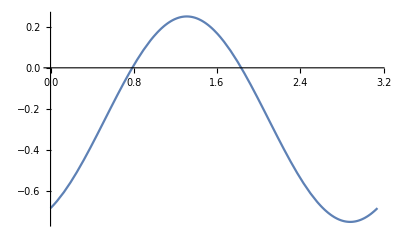
Rasterize⟦-Graphics-⟧

```mathematica
Rasterize[[Plot[Sin[x+Pi/4]Sin[x-Pi/12]-1/2,{x,0,Pi}]]]
```

```mathematica
FindRoot[Sin[x+Pi/4]Sin[x-Pi/12]-1/2,{x,0.8}]
```

{x→0.785398}

```mathematica
FindRoot[Sin[x+Pi/4]Sin[x-Pi/12]-1/2,{x,1.8}]
```

{x→1.8326}

故解为以上两个数加k π，k为整数。

7. (4)

```mathematica
Rasterize[Plot[6Sin[x]^2+3Sin[x]Cos[x]-5Cos[x]^2-2,{x,0,Pi}]]
```

-Graphics-

```mathematica
FindRoot[6Sin[x]^2+3Sin[x]Cos[x]-5Cos[x]^2-2,{x,0.5}]
```

{x→0.785398}

```mathematica
FindRoot[6Sin[x]^2+3Sin[x]Cos[x]-5Cos[x]^2-2,{x,2}]
```

{x→2.08994}

故解为以上两个数加k π，k为整数。

11. (1)

```mathematica
LinearProgramming[{-3,-2},{{-1,2},{3,2},{1,-1}},{{4,-1},{14,-1},{3,-1}}]
```

{4,1}

```mathematica
{4,1}.{3,2}
```

14

11. (2)

```mathematica
LinearProgramming[{2,3,4},{{1,2,-1},{1,1,-1},{0,1,2}},{10,60,12},{0,0,1}]
```

{51,10,1}

```mathematica
{{1,2,-1},{1,1,-1},{0,1,2}}.{51,10,1}
```

{70,60,12}

故取不到最小值。

12. (1)

```mathematica
sol=NDSolve[{y''[x]+y[x]==Cos[x],y[0]==0,y'[0]==0},y,{x,0,20}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Rasterize[Plot[Evaluate[y[x]/.sol],{x,0,20}]]
```

-Graphics-

12. (2)

```mathematica
sol=NDSolve[{D[u[t,x],t]==D[u[t,x],{x,2}],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0,5}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Rasterize[Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}]]
```

-Graphics-

# 习题6

1. (1)

```mathematica
Rasterize[Plot[1+x+x^3,{x,-100,100},AxesLabel->{"x","y"},Axes->{False,True}]]
```

-Graphics-

1. (2)

```mathematica
Rasterize[Plot[(x-1)(x-2)^2,{x,-70,70},Mesh->Full,MeshStyle->{Red, Blue},MeshShading->{Black}]]
```

-Graphics-

1. (3)

```mathematica
Rasterize[Plot[x+Sin[x],{x,-10,10},Method->{"AxesInFront" -> True},AspectRatio->1/2]]
```

-Graphics-

1. (4)

```mathematica
Rasterize[Plot[x^2Sin[x^2],{x,-60,60},Filling->Bottom,PlotStyle->Gray]]
```

-Graphics-

2. (1)

```mathematica
y[x_]:=x^2(x-1)/(x+1)^2;
Rasterize[Plot[{y[x],y'[x]},{x,-100,100}]]
```

-Graphics-

2. (2)

```mathematica
y[x_]:=Sin[x]/(1+x^2);
Rasterize[Plot[{y[x],y'[x]},{x,-90,90}]]
```

-Graphics-

3. (1)

```mathematica
Rasterize[ParametricPlot[{(t+1)^2/4,(t-1)^2/4},{t,-6,6}]]
```

-Graphics-

3. (2)

```mathematica
Rasterize[ParametricPlot[{Cos[2t],Cos[3t]},{t,-Pi,Pi}]]
```

-Graphics-

3. (3)

```mathematica
Rasterize[ParametricPlot[{t*Log[t],Log[t]/t},{t,0,6Pi}]]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics-

4. (1)

```mathematica
Rasterize[Plot3D[E^(-x^2-y^2),{x,-3,3},{y,-3,3}]]
```

-Graphics-

4. (2)

```mathematica
Rasterize[Plot3D[Sin[x+Cos[y]],{x,-6,6},{y,-6,6}]]
```

-Graphics-

4. (3)

```mathematica
Rasterize[Plot3D[(x^2-y^2)/(x^3+y^3),{x,-10,10},{y,-10,10}]]
```

-Graphics-

5. (1)

```mathematica
Rasterize[Plot3D[x/(E^(x^2+y^2)),{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},2<x^2+y^2<3]]]
```

-Graphics-

5. (2)

```mathematica
Rasterize[Plot3D[1/(y^2-x^3+3x-3),{x,-3,3},{y,-3,3},RegionFunction->Function[{x,y,z},0<Mod[x^2+y^2,2]<1]]]
```

-Graphics-

6. (1)

```mathematica
Rasterize[ParametricPlot3D[{Sin[t],Cos[t],t/3},{t,0,15}]]
```

-Graphics-

6. (2)

```mathematica
Rasterize[ParametricPlot3D[{u*Sin[t],u*Cos[t],t/3},{t,0,15},{u,-1,1}]]
```

-Graphics-

6. (3)

```mathematica
Rasterize[ParametricPlot3D[{Sin[a]Cos[b],Sin[a]Sin[b],Cos[a]},{a,0,Pi/2},{b,0,2Pi}]]
```

-Graphics-

6. (4)

```mathematica
Rasterize[ParametricPlot3D[{Sin[a]Cos[b],Sin[a]Sin[b],Cos[a]},{a,0,Pi},{b,Pi/2,3Pi/2}]]
```

-Graphics-

7.

```mathematica
ContourPlot[Sin[x*Cos[y]],{x,-10,10},{y,-5,5}]
```

-Graphics-

```mathematica
Rasterize[DensityPlot[Sin[x*Cos[y]],{x,-10,10},{y,-5,5}]]
```

-Graphics-

8.

```mathematica
list = {1.2,3.3,2.2,5.5,7.7,9.9};
Rasterize[BarChart[list]]
```

-Graphics-

```mathematica
PieChart[list]
```

-Graphics-

9.

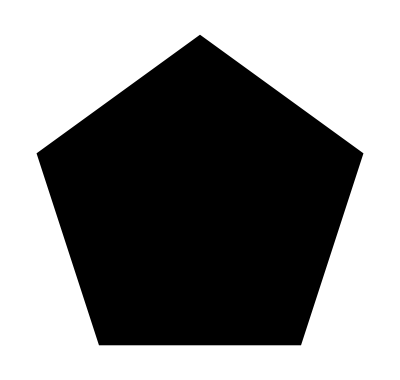

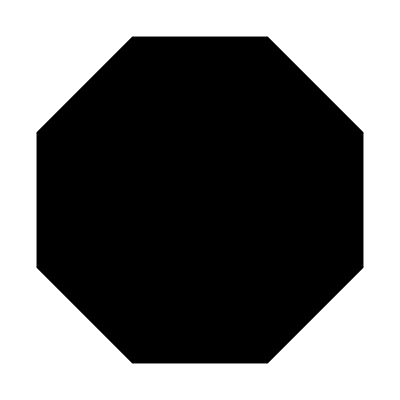

```mathematica
Rasterize[Graphics[RegularPolygon[5]]]
Rasterize[Graphics[RegularPolygon[8]]]
```

10. (1)

```mathematica
Rasterize[PolarPlot[{Sqrt[Cos[2θ]],-Sqrt[Cos[2θ]]},{θ,-Pi/2,Pi/2}]]
```

-Graphics-

10. (2)

```mathematica
Rasterize[PolarPlot[1-Cos[θ],{θ,0,2Pi}]]
```

-Graphics-

# 第6章-图表、图与动画

```mathematica
Rasterize[RectangleChart[{{1,1},{2,1},{3,2},{2,2},{5,1}},ChartStyle->Thickness[.5],ChartElementFunction->"FadingRectangle"]]
```

-Graphics-

```mathematica
Rasterize[RectangleChart3D[{{{2,3,3},{1,2,2},{1,1,1}},{{1,3,2},{2,1,1}}},ChartLabels->Placed[{"X1","X2","X3"},Center]]]
```

-Graphics-

```mathematica
Rasterize[SectorChart[{{1,2},{2,1},{3,1}},SectorOrigin->{Automatic,1},ChartStyle->"Pastel"]]
```

-Graphics-

```mathematica
Rasterize[SectorChart3D[{{2,2,3},{2,1,2},{1,2,1}},ChartStyle->"DarkRainbow",ChartLegends->{"a","b","c"}]]
```

-Graphics-

```mathematica
Rasterize[Histogram[RandomVariate[NormalDistribution[0,1],200],Automatic,"Probability"]]
```

-Graphics-

```mathematica
Rasterize[Histogram3D[RandomVariate[NormalDistribution[0,1],{100,2}],10,ChartElements->Graphics3D[Cylinder[]]]]
```

-Graphics-

```mathematica
Rasterize[RegionPlot[x^2+y^3<2,{x,-2,2},{y,-2,2},ColorFunction->"SunsetColors",BoundaryStyle->None]]
```

-Graphics-

```mathematica
Rasterize[RegionPlot3D[x^2+y^3-z^2>0,{x,-2,2},{y,-2,2},{z,-2,2},PlotPoints->35,PlotRange->All]]
```

-Graphics-

```mathematica
Rasterize[VectorPlot[{y,-x^2},{x,-3,3},{y,-3,3},StreamPoints->10,StreamScale->Full]]
```

-Graphics-

```mathematica
Rasterize[VectorPlot3D[{x,-y,z},{x,0,1},{y,0,1},{z,0,1},VectorColorFunction->Hue,VectorScale->{Automatic,Scaled[0.3]}]]
```

-Graphics-

```mathematica
Rasterize[StreamPlot[{-x^2+y,y^3},{x,0,1},{y,0,2},StreamStyle->Yellow,FrameStyle->LightGray,Background->Black]]
```

-Graphics-

```mathematica
Rasterize[StreamPlot[{-y^3-x^2,x+y},{x,0,1},{y,-1,1},BoundaryStyle->None,FrameLabel->{x,y}]]
```

-Graphics-

```mathematica
Rasterize[MatrixPlot[{{1,0,2},{3,0,2},{4,6,0}},ColorFunction->"Monochrome",Background->LightBlue]]
```

-Graphics-

```mathematica
Rasterize[MatrixPlot[{{1,10,1},{100,0,1},{-10,0,-1}},PlotRange->{-1,1},ClippingStyle->{Green,Yellow}]]
```

-Graphics-

```mathematica
Rasterize[TreePlot[KaryTree[9,2],PlotStyle->Directive[PointSize[Large],Red]]]
```

-Graphics-

```mathematica
Rasterize[TreePlot[Flatten[Table[{i-> 2i+j-1},{j,2},{i,2^7-1}]],Center,LayerSizeFunction->(#1 &)]]
```

-Graphics-

```mathematica
Rasterize[GraphPlot[{{0,1,1,1,0},{1,0,1,0,1},{1,1,0,0,1},{1,0,0,1,1},{0,1,1,1,0}},GraphLayout->{"CircularMultipartiteEmbedding", "VertexPartition"->{2,1,2}}]]
```

-Graphics-

```mathematica
Rasterize[GraphPlot[{1->2,2->3,3->4,4->1,2->4},DirectedEdges-> True,PlotStyle->Directive[PointSize[Large],Gray]]]
```

-Graphics-

```mathematica
Animate[Plot[t*x^3-t*x+1,{x,-3,3}],{t,-1,1,0.1}]
```

```mathematica
Animate[Expand[(x+1)^t],{t,1,10,1}]
```

```mathematica
ListAnimate[Table[Plot[Sin[n x],{x,0,10}],{n,5}]]
```

```mathematica
ListAnimate[Range[10],AnimationRate->{0.5,1},AnimationRunning->False]
```

# 习题7

1.

```mathematica
DeriOut[f_]:={f[x],D[f[x],x],D[f[x],{x,2}]}
```

```mathematica
(#1^2)&//DeriOut
```

{x^2,2 x,2}

3.

```mathematica
DiagUp[n_]:=Table[(i==j)*i,{i,n},{j,n}]/.{True->1,False->0}
```

```mathematica
MatrixForm[DiagUp[4]]
```

(1 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 3 | 0
0 | 0 | 0 | 4)

5.

```mathematica
MatrixA[n_]:=Table[If[j≥i,j-i,j],{i,n},{j,n}]
```

```mathematica
MatrixForm[MatrixA[4]]
```

(0 | 1 | 2 | 3
1 | 0 | 1 | 2
1 | 2 | 0 | 1
1 | 2 | 3 | 0)

6.

```mathematica
SeqCount[A_]:=If[Length[A]==1,0,Count[Sign[A-A[[1]]],1]+SeqCount[Rest[A]]]
```

```mathematica
SeqCount[{1,2,4,5,3}]
```

8

```mathematica
InvCount[A_]:=If[Length[A]==1,0,Count[Sign[A-A[[1]]],-1]+InvCount[Rest[A]]]
```

```mathematica
InvCount[{1,2,4,5,3}]
```

2

7.

```mathematica
DrawPolygon[n_]:=Graphics[RegularPolygon[n]]
```

```mathematica
Rasterize[DrawPolygon[4]]
```

-Graphics-

10.

```mathematica
BasicOperate[A_,row_,type_,param_]:=
If[row,
If[type==1,Table[If[i==param[[1]],A[[i]]*param[[2]],A[[i]]],{i,Length[A]}],
If[type==2,Table[If[i==param[[1]],A[[param[[2]]]],If[i==param[[2]],A[[param[[1]]]],A[[i]]]],{i,Length[A]}],
Table[If[i==param[[1]],A[[i]]+param[[3]]*A[[param[[2]]]],A[[i]]],{i,Length[A]}]]],Transpose[BasicOperate[Transpose[A],True,type,param]]];
```

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
MatrixForm[BasicOperate[A,True,3,{3,1,-2}]]
```

(1 | 2 | 3
4 | 5 | 6
5 | 4 | 3)

```mathematica
MatrixForm[BasicOperate[A,False,2,{1,2}]]
```

(2 | 1 | 3
5 | 4 | 6
8 | 7 | 9)

```mathematica
MatrixForm[BasicOperate[A,False,1,{3,0.5}]]
```

(1 | 2 | 1.5
4 | 5 | 3.
7 | 8 | 4.5)

# 习题8

1.

```mathematica
Map[Print,Partition[Flatten[{Select[Table[i,{i,100,1000}],Mod[#,3]==0||Mod[#,11]==0&],Table[Null,4]}],5]];
```

{102,105,108,110,111}

{114,117,120,121,123}

{126,129,132,135,138}

{141,143,144,147,150}

{153,154,156,159,162}

{165,168,171,174,176}

{177,180,183,186,187}

{189,192,195,198,201}

{204,207,209,210,213}

{216,219,220,222,225}

{228,231,234,237,240}

{242,243,246,249,252}

{253,255,258,261,264}

{267,270,273,275,276}

{279,282,285,286,288}

{291,294,297,300,303}

{306,308,309,312,315}

{318,319,321,324,327}

{330,333,336,339,341}

{342,345,348,351,352}

{354,357,360,363,366}

{369,372,374,375,378}

{381,384,385,387,390}

{393,396,399,402,405}

{407,408,411,414,417}

{418,420,423,426,429}

{432,435,438,440,441}

{444,447,450,451,453}

{456,459,462,465,468}

{471,473,474,477,480}

{483,484,486,489,492}

{495,498,501,504,506}

{507,510,513,516,517}

{519,522,525,528,531}

{534,537,539,540,543}

{546,549,550,552,555}

{558,561,564,567,570}

{572,573,576,579,582}

{583,585,588,591,594}

{597,600,603,605,606}

{609,612,615,616,618}

{621,624,627,630,633}

{636,638,639,642,645}

{648,649,651,654,657}

{660,663,666,669,671}

{672,675,678,681,682}

{684,687,690,693,696}

{699,702,704,705,708}

{711,714,715,717,720}

{723,726,729,732,735}

{737,738,741,744,747}

{748,750,753,756,759}

{762,765,768,770,771}

{774,777,780,781,783}

{786,789,792,795,798}

{801,803,804,807,810}

{813,814,816,819,822}

{825,828,831,834,836}

{837,840,843,846,847}

{849,852,855,858,861}

{864,867,869,870,873}

{876,879,880,882,885}

{888,891,894,897,900}

{902,903,906,909,912}

{913,915,918,921,924}

{927,930,933,935,936}

{939,942,945,946,948}

{951,954,957,960,963}

{966,968,969,972,975}

{978,979,981,984,987}

{990,993,996,999,Null}

2.

```mathematica
f[A_]:=A//.{a___,x_,b___,x_,c___}:>{a,x,b,c}
```

```mathematica
f[{1,2,3,41,2,34,123,21,21,2,12,2,2,2,3,3,4,4,4,2,1,1,1}]
```

{1,2,3,41,34,123,21,12,4}

4.

```mathematica
pol[x_]:=x^3-2x^2+7x+4;res[0]=-1;res[1]=1;
res[n_]:=(res[n]=(res[n-2]*pol[res[n-1]]-res[n-1]*pol[res[n-2]])/(pol[res[n-1]]-pol[res[n-2]]));
(*用res[n]=进行记忆，避免重复计算*)
Module[{n},n=2;While[Abs[res[n]-res[n-1]]>10^(-16),n++];N[res[n]]]
```

-0.48712

6.

```mathematica
f[x_]:=Switch[True,x≤-20,Sin[x],20≤x,Cos[x],True,x^2];
A=RandomReal[{-100,100},30];
Rasterize[ListPlot[Map[{#,f[#]}&,A]]]
```

-Graphics-

9.

```mathematica
Eigensystem[RandomReal[{-10,10},{4,4}]]
```

{{-12.0071,4.79559+6.32987 ⅈ,4.79559-6.32987 ⅈ,6.59912},{{0.446724+0. ⅈ,-0.631906+0. ⅈ,-0.0245104+0. ⅈ,-0.632875+0. ⅈ},{-0.57695-0.106587 ⅈ,-0.629032+0. ⅈ,-0.149185-0.410455 ⅈ,-0.257897-0.0533499 ⅈ},{-0.57695+0.106587 ⅈ,-0.629032+0. ⅈ,-0.149185+0.410455 ⅈ,-0.257897+0.0533499 ⅈ},{-0.656324+0. ⅈ,-0.529027+0. ⅈ,-0.147861+0. ⅈ,-0.51721+0. ⅈ}}}

12.

```mathematica
L2[A_]:=Sqrt[Max[Eigenvalues[Transpose[A].A]]];
L2[{{1,2,3},{4,5,6}}]
```

√(1/2 (91+√8065))

16.

```mathematica
Newton[f_,x0_,n_]:=If[n==0,x0,N[(x-f[x]/D[f[x],x])/.x->Newton[f,x0,n-1]]];
Newton[#^2-2&,1,100]
```

1.41421

18.

```mathematica
StarZero[n_]:=MatrixForm[Table[If[OddQ[Min[{i,j,n-i+1,n-j+1}]],"*",0],{i,n},{j,n}]]
```

```mathematica
StarZero[7]
```

(* | * | * | * | * | * | *
* | 0 | 0 | 0 | 0 | 0 | *
* | 0 | * | * | * | 0 | *
* | 0 | * | 0 | * | 0 | *
* | 0 | * | * | * | 0 | *
* | 0 | 0 | 0 | 0 | 0 | *
* | * | * | * | * | * | *)